# Interpolación de Lagrange

## Generación de puntos

```mathematica
a = 1; b = 5;
datos = Table[{x,N[x Sin[x]]},{x,a,b,1}]
```

{{1,0.841471},{2,1.81859},{3,0.42336},{4,-3.02721},{5,-4.79462}}

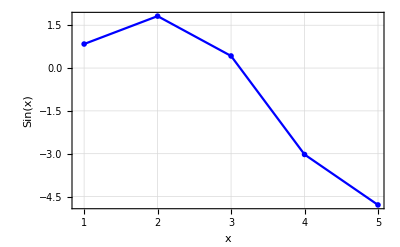

```mathematica
ListLinePlot[datos,
PlotTheme->"Monochrome",FrameLabel->{Style["x",15], Style["Sin(x)",15]}, BaseStyle->FontSize->13,PlotRangePadding->Automatic,GridLines->Automatic,Frame->True,PlotRange->All,PlotStyle->{Blue}
]
```

## Base de Lagrange

```mathematica
LagrangeBaseElements[xs_,i_]:=Table[If[i≠ j,(x-xs[[j+1]])/(xs[[i+1]]-xs[[j+1]]),1],{j,0,Length[xs]-1}];
LagrangeBase[xs_,i_]:=Apply[Times,LagrangeBaseElements[xs,i]];
```

```mathematica
LagrangeBase[datos[[All,1]],0]
```

1/24 (2-x) (3-x) (4-x) (5-x)

```mathematica
Total@Table[LagrangeBase[datos[[All,1]],i],{i,0,4}]
```

1/24 (2-x) (3-x) (4-x) (5-x)+1/6 (3-x) (4-x) (5-x) (-1+x)+1/4 (4-x) (5-x) (-2+x) (-1+x)+1/6 (5-x) (-3+x) (-2+x) (-1+x)+1/24 (-4+x) (-3+x) (-2+x) (-1+x)

```mathematica
Expand@Total@Table[LagrangeBase[datos[[All,1]],i],{i,0,4}]
```

1

```mathematica
LagrangeInterpolate[data_]:=Expand[data[[All,2]].Table[LagrangeBase[data[[All,1]],i],{i,0,Length[data]-1}]];
```

```mathematica
LagrangeInterpolate[datos]
```

0.596435-2.01119 x+3.48644 x^2-1.37278 x^3+0.142561 x^4

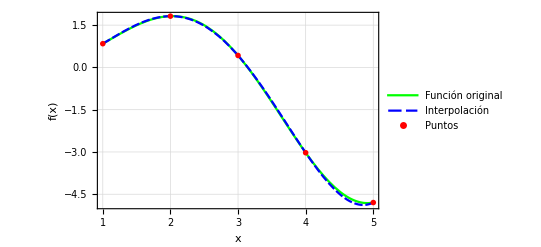

```mathematica
Show[
Plot[
{x Sin[x],0.5964351621647346-2.011191348684978 x+3.486441267683059 x^2-1.3727753574753927 x^3+0.1425612611204672 x^4},
{x,a,b},
PlotTheme->"Monochrome",FrameLabel->{Style["x",15], Style["f(x)",15]}, BaseStyle->FontSize->13,PlotRangePadding->Automatic,GridLines->Automatic,Frame->True,PlotRange->All,PlotStyle->{Green,Blue},PlotLegends->{"Función original","Interpolación"}
],
ListPlot[datos,
PlotTheme->"Monochrome",BaseStyle->FontSize->13,PlotRangePadding->Automatic,GridLines->Automatic,Frame->True,PlotRange->All,PlotStyle->{Red},PlotLegends->{"Puntos"}
]
]
```